# PNEUMONIA: MODEL FIT

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
data=Import["Datasheet_combined.xlsx",{"Data","Pneu_all"}]; (*import data*)
data = data[[All,2;;]]; 
years = data[[1]];
tt = Length[years]; 
nop = Round[data[[-1]][[1]]]; (*# of pathogens*)
isolates = data[[2;;2*nop+1;;2]]; 
resistance = data[[3;;2*nop+1;;2]];
rfreq =Quiet[
resistance/isolates]/.Indeterminate-> 0; (*resistance frequency*)
pathogens=data[[2*nop+3]][[1;;nop]]; (*pathogen headers*)
carbcons =  data[[2*nop+4]]; (*CBP consumption (DDDs): total*)
conbreak = data[[2*nop+6;;3*nop+5]]; (*CBP consumption by pathogen*)
prev=data[[-2]]; (*pneumonia prevalence*)
cbpp= data[[2*nop+5]]; (*CBP prescribed to that diagnosis*)
cbp =Table[cbpp*carbcons*conbreak[[i]],{i,1,nop}];
(*CBP consumption: pneumonia only & by pathogen*)
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

### Model Fitting

Fit r_0 and k_s using a binomial maximum likelihood function. Fix θ based on literature.

```mathematica
θ=-0.02; (*Di Luca, 2017*)

max  = PadRight[{},nop,Null];
fr0 = max; fks=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]]}}=NMaximize[{Lik[r0,ks],0<r0<1},{r0,ks}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;

(*create table of fitted values*)
params= Join[{max},{fr0},{fks}];
headings1=Prepend[params,pathogens];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s"}}];
Grid[headings2,Frame-> All]
```

| PA | AB | KP | SP
Likelihood | -86.7601 | -75.8286 | -44.8812 | -47.9409
r0 | 0.174762 | 0.283851 | 0.0645429 | 0.334239
k_s | 7.36985 | 68.5353 | -32.3568 | -16.0544

### Sampling and Bayesian Melding

#### Functions

```mathematica
fonGrid[x_,y_,f_]:=Module[{n,m,fvals},
n=Length[x];
m=Length[y];
fvals=Table[0,{m},{n}];(*preallocate fvals*)
Do[Do[fvals[[i,j]]=f[x[[j]],y[[i]]];,{i,1,m}];,{j,1,n}];
fvals]
(*x is an n-by-1 vector*)
(*y is an n-by-1 vector*)
(*f is a scalar function of two variables*)
(*fvals is an m-by-n matirx where fVals[[i,j]]=f[x[[j]],y[[i]]]*)

repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
```

#### Initialization for parameter estimates and plots

```mathematica
r0T = PadRight[{},nop,Null]; 
ksT = PadRight[{},nop,Null]; 
plotD  = PadRight[{},nop,Null]; (*data*)
plotM  = PadRight[{},nop,Null]; (*model fit*)

nif = 0.1; (* noise around mle values for bayesian melding prior*)
nb=100; (*number of parameter values randomly selected for Bayesian melding step*)
sb=1000; (*number of weighted samples for Bayesian melding step*)
```

#### Bayesian melding for each pathogen

```mathematica
For[i=1,i≤ nop,i++,
iso = isolates[[i]];
resis = resistance[[i]];
a = cbp[[i]];

(*Take nb samples for Subscript[r, 0] and Subscript[k, s]*)
r0s = RandomReal[{(1-nif)*fr0[[i]],(1+nif)*fr0[[i]]},nb]; (*Subscript[r, 0] samples*)
kss = RandomReal[{(1-nif)*fks[[i]],(1+nif)*fks[[i]]},nb]; (*Subscript[k, s] samples*)

lik = fonGrid[r0s,kss,Lik]; (*Calculates a matrix of loglikelihood values for Subscript[r, 0], Subscript[k, s] values*)
ls = Exp[lik]; (*Exponential to get likelihood*)
w = ls/Total[Total[ls]]; (*Calculate weights for likelihood*)
lb =ArrayReshape[ls,{1,nb^2}][[1]]; (*Flatten the likelihood to get a vector*)
wb = ArrayReshape[w,{1,nb^2}][[1]]; (*Flatten the weights to get a vector*)

r0b = Table[repeat[r0s[[i]],nb],{i,1,nb}];(*Resize r0 to match likelihood vector: repeat 1st term of r0 vector n times, then 2nd term n times, etc.*)
ksb = PadRight[kss,nb^2,kss];(*Resize ks to match size of likelihood vector: repeat ks vector n times*)

ind = RandomChoice[wb->Range[nb^2],sb];(*Choose mb indices from 1 to nb^2 based on weights(importance sampling with replacement)*)
r0b = r0b[[ind]];ksb = ksb[[ind]]; lb = lb[[ind]]; (*Get posterior parameters (Subscript[r0, v],Subscript[ks, v]) and likelihood (Subscript[l, v]) based on melding*)
od = Ordering[lb];(*sort the likelihood values in order to get confidence intervals*)
r0T[[i]]=r0b[[od]];ksT[[i]]=ksb[[od]]];(*Order parameters in the same order as sorted likelihoods*)
```

### Plots and Projections

#### Model fit plots

```mathematica
t=Range[1,tt]; 
pathogens = {"Pseudomonas aeruginosa","Acinetobacter baumanii","Klebsiella pneumoniae","Streptococcus pneumoniae"};

nos=0.95*sb; (*number of 95% CI parameters sampled*)
rm=ConstantArray[Null,{nop,sb}]; (*initialize resistance from model output*)
rmbest=ConstantArray[Null,nop]; (*best fit*)
rmin=ConstantArray[Null,{nop,15}];rmax=ConstantArray[Null,{nop,15}];
rfit=ConstantArray[Null,nop];
res=ConstantArray[Null, nop]; (*resistance frequency data*)
```

```mathematica
For[i=1,i≤nop,i++,
r0p =r0T[[i]];ksp = ksT[[i]]; (*save 95% CI parameters for each pathogen*)
res[[i]]= Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)
For[j=1,j≤sb,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],rm[[i]][[j]]= Table[r[k,r0p[[j]],ksp[[j]],θ],{k,1,tt}]}]; (*generate model outputs for sampled parameter sets*)
rmbest[[i]]=Table[r[k,fr0[[i]],fks[[i]],θ],{k,1,tt}];(*model output under best fit*)
rmin[[i]] = Table[Min[rm[[i]][[51;;1000,r]]],{r,1,tt}]; rmax[[i]] = Table[Max[rm[[i]][[51;;1000,r]]],{r,1,tt}];(*find min and max parameter sets*)

rfill = {rmin[[i]],rmax[[i]]};
rfit[[i]]= Table[Transpose@{years,rfill[[i]]},{i,1,2}];
plotD[[i]] = ListPlot[res[[i]],PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,AxesOrigin-> {years[[1]],0}];
plotM[[i]] =ListLinePlot[Table[rfit[[i]][[j]],{j,2}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesStyle->Directive[14],PlotRange->All,PlotLabel->Style[pathogens[[i]],Italic,16],Filling->{1->{2}} ,AxesOrigin-> {years[[1]],0}];]
```

#### Model projections

#### Status quo:

1. Maintain most recent consumption levels until end of projections (t_f); 
2. Maintain linear trend of increasing consumption levels until end of projections (t_f).

```mathematica
ti=years[[-1]]+1; (*projections begin at year Subscript[t, i]*)
tf =2030; (*projection until year Subscript[t, f]*) 
pyears = Range[ ti,tf]; (*vector of years from ti to tf*)
nyears = Length[pyears];(*# of years to project across*)

cbp0 = data[[-3,1]]*carbcons[[-1]]; (*current CBP consumption for pneumonia (all pathogens)*)
projSQ=Table[ConstantArray[cbp[[i]][[-1]],nyears],{i,1,nop}];
cbpSQ = Table[Join[cbp[[i]],projSQ[[i]]],{i,1,nop}];
```

#### Interventions:

```mathematica
sy=2018; ey=2020; (*start of intervention, year of achieving full reduction*)
sqyears=Range[ti,sy-1]; (*status quo years prior to intervention start*)
ncy=Length[sqyears]; (*# sq years before beginning intervention*)
niy=ey-sy+1;  (*# intervention years prior to reaching full reduction*)

inapp = 0.5; (*reduction in inappropriate therapy*)
projI=Table[Join[
ConstantArray[cbp[[i]][[-1]],ncy],
Range[cbp[[i]][[-1]],cbp[[i]][[-1]]*(1-inapp),-(cbp[[i]][[-1]]*inapp)/(niy-1)],
ConstantArray[cbp[[i]][[-1]]*(1-inapp),Round[nyears-ncy-niy]]],
{i,1,nop}];
cbpI=Table[Join[cbp[[i]],projI[[i]]],{i,1,nop}];
```

#### Projected resistance frequencies:

```mathematica
(*initalize stored values*)
rSQ =ConstantArray[Null,{nop,sb}]; (*resistance projections for status quo*)
rSQbest=ConstantArray[Null,nop]; (*resistance projections for SQ with best fit*)
rSQm=ConstantArray[Null,nop];rSQM=ConstantArray[Null,4]; (*min and max*)
fitS=ConstantArray[Null,nop]; (*uncertainty band*)
rI=ConstantArray[Null,{nop,sb}];(*resistance projections for intervention*)
rIbest=ConstantArray[Null,nop]; (*best fit*)
rIm=ConstantArray[Null,nop]; rIM=ConstantArray[Null,nop]; (*min and max resistance values*)
fitI=ConstantArray[Null,nop]; (*uncertainty band*)

(*intialize plots*)
ploty=Range[years[[-1]],tf];
plotS  = ConstantArray[Null,nop]; (*status quo projections*)
plotI  = ConstantArray[Null,nop]; (*intervention projections*)

(*status quo projections*)
For[i=1,i≤ nop,i++, (*# pathogens*)
r0p =r0T[[i]];ksp = ksT[[i]];(*save 95% CI parameters for each pathogen*)
For[j=1,j≤sb,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],rSQ[[i]][[j]]= Table[r[k,r0p[[j]], ksp[[j]],θ],{k,tt,tt+nyears}]}];
rSQm [[i]]= Table[Min[rSQ[[i]][[51;;1000,r]]],{r,1,nyears+1}]; rSQM [[i]]= Table[Max[rSQ[[i]][[51;;1000,r]]],{r,1,nyears+1}]; (*generate model outputs for sampled parameter sets*)
rSQbest[[i]]=Table[r[k,fr0[[i]],fks[[i]],θ],{k,tt,tt+nyears}];
rSQfill = Table[{rSQm[[k]],rSQM[[k]]},{k,1,nop}];
fitS [[i]]= Table[Transpose@{ploty,rSQfill[[i]][[k]]},{k,1,2}];plotS[[i]] =ListLinePlot[Table[fitS[[i]][[j]],{j,2}],PlotStyle->{RGBColor[0.75,0.75,0.75]},PlotRange->All,Filling->{1->{2}},AxesOrigin-> {years[[1]],0}];]; (*SQ plots per pathogen*)

(*intervention projections*)
For[i=1,i≤ nop,i++, (*# pathogens*)
r0p =r0T[[i]];ksp = ksT[[i]];(*save 95% CI parameters for each pathogen*)
For[j=1,j≤sb,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[i]],rI[[i]][[j]]= Table[r[k,r0p[[j]], ksp[[j]],θ],{k,tt,tt+nyears}]}];
rIm [[i]]= Table[Min[rI[[i]][[51;;1000,r]]],{r,1,nyears+1}]; rIM [[i]]= Table[Max[rI[[i]][[51;;1000,r]]],{r,1,nyears+1}]; (*generate model outputs for sampled parameter sets*)
rIbest[[i]]=Table[r[k,fr0[[i]],fks[[i]],θ],{k,tt,tt+nyears}];
rIfill = Table[{rIm[[k]],rIM[[k]]},{k,1,nop}];
fitI[[i]] = Table[Transpose@{ploty,rIfill[[i]][[k]]},{k,1,2}];plotI[[i]] =ListLinePlot[Table[fitI[[i]][[j]],{j,2}],PlotStyle->{RGBColor[0.3,0.5,0.75]},PlotRange->All,Filling->{1->{2}},AxesOrigin-> {years[[1]],0}];];
```

#### Projected Plots

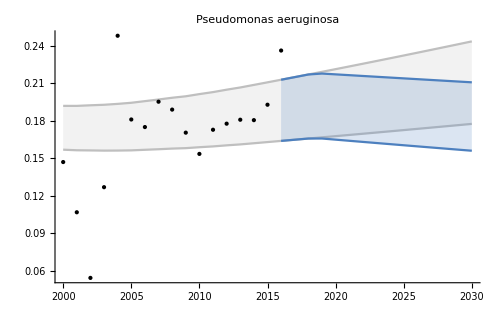
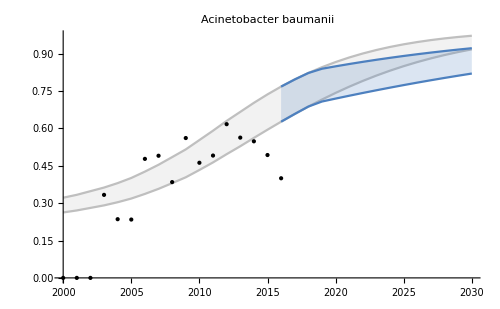
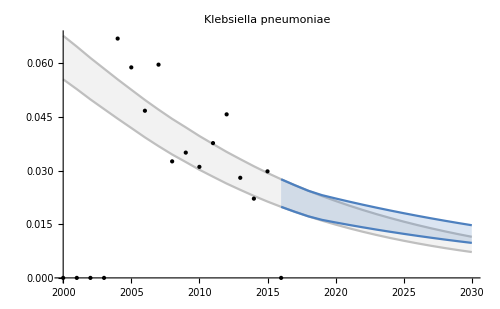
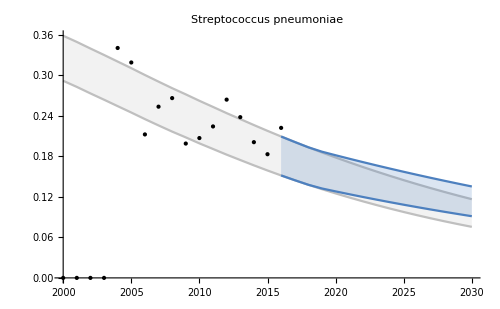

```mathematica
plotsM=ConstantArray[Null,nop];
For[i=1,i≤ nop, i++,plotsb[[i]]=Show[plotM[[i]],plotD[[i]],plotS[[i]],plotI[[i]],PlotRange->All,Axes->True,ImageSize->500]]
plotsb
Export["resp model plots.pdf",plotsM];
```

```mathematica
(*New Plots- No uncertainty*)
mf=Table[Transpose@{years,rmbest[[k]]},{k,1,nop}]; (*model fit data w/ years*)
sqf=Table[Transpose@{ploty,rSQbest[[k]]},{k,1,nop}]; (*status quo data w/ years*)
sqdata=Table[Join[mf[[k]],sqf[[k]]],{k,1,nop}]; (*data to plot*)
plotSQf=Table[ListLinePlot[sqdata[[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[k]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],{k,1,nop}];

yminSQ=Table[Min[rmbest[[i]],rIbest[[i]]]-0.05,{i,1,nop}]; (*where to put the x axis*)

if=Table[Transpose@{ploty[[2;;]],rIbest[[k]][[2;;]]},{k,1,nop}]; (*intervention fit data*)
plotIf=Table[ListLinePlot[if[[k]],FrameLabel->{{x,Year},{y,Resistance}},PlotRange->All,PlotStyle-> {Thick},AxesOrigin-> {years[[1]],0}],{k,1,nop}];
```

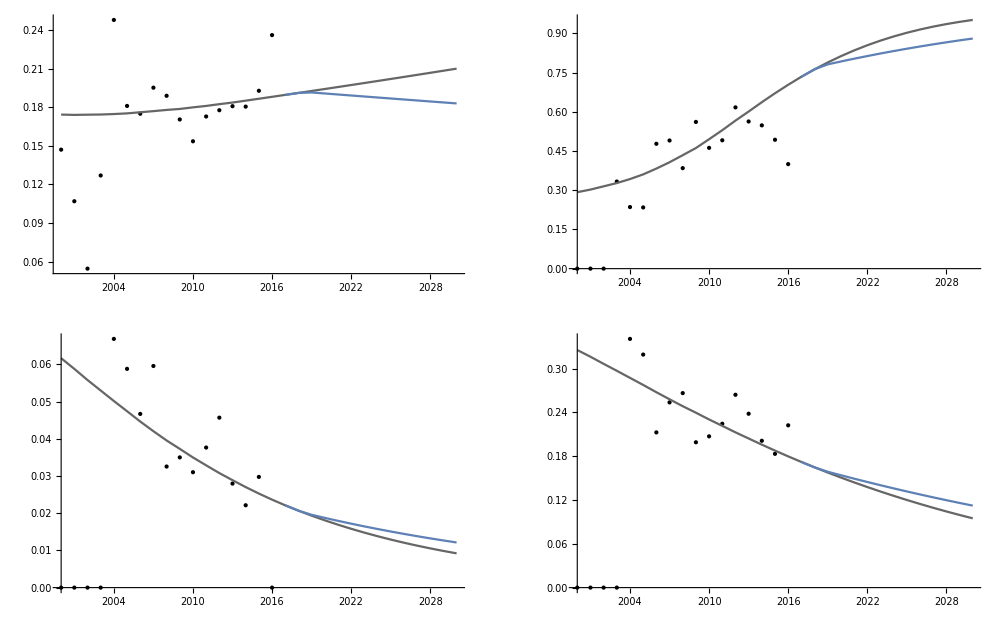
-Graphics-Resistance Frequency Projections with Various InterventionsResistance frequencyYear

```mathematica
(*Create graphics grid*)
plotsF=Panel[GraphicsGrid[{{Show[plotD[[1]],plotSQf[[1]],plotIf[[1]],AxesStyle->Directive[14],AxesOrigin-> {2000,0}, PlotRange->All],Show[plotD[[2]],plotSQf[[2]],plotIf[[2]],PlotRange->All,Axes->True,AxesStyle->Directive[14],AxesOrigin->{2000,0}]},{Show[plotD[[3]],plotSQf[[3]],plotIf[[3]],AxesStyle->Directive[14],AxesOrigin->{2000,0},PlotRange->All],Show[plotD[[4]],plotSQf[[4]],plotIf[[4]],AxesStyle->Directive[14],AxesOrigin->{2000,0},PlotRange->All]}},ImageSize->1000],{Style["Resistance Frequency Projections with Various Interventions","Panel",24,Background->White],Style[Rotate["Resistance frequency",90 Degree],"Panel",18,Background->White],Style["Year","Panel",18,Background->White]},{{Top,Center},{Left,Center},{Bottom,Center}},Appearance->"Frameless",Background->White]

Export["resp model plots best fit.pdf",plotsF];
```

#### Export data

```mathematica
(*with uncertainty*)
Export["resp model.xls",{"resistance"-> resistance, "isolates" -> isolates,"rfit"-> rfit,"rmbest"-> rmbest, "fitS"-> fitS, "rSQbest"-> rSQbest, "fitI"-> fitI, "rIbest"-> rIbest}];
```

## Switch Year

### Parameters

```mathematica
(*associated mortality rates {PA,AB,KP,EA/C}*)

m={{0.1050,0.084},{ 0.0999,0.086}}; (*cbp v. alternative; mortality  + resis; mortality + suscep*)
```

### Calculating the switch year

```mathematica
yswitch=NSolve[x*m[[1]][[1]]+(1-x)*m[[1]][[2]]==x*m[[2]][[1]]+(1-x)*m[[2]][[2]],x];
yswitch=yswitch[[1]][[1]][[2]];
(*set mortality from CBP equal to mortality from alternative to solve for resistance where we need to switch prescription*)
```

### Applying the switch year

#### Calculating the switch year

```mathematica
y=Range[2000,tf];
switchdata=Table[Transpose@{y,ConstantArray[yswitch,Length[y]]},{i,1,nop}];

ymin=Table[Min[rmbest[[i]],rSQbest[[i]],rIbest[[i]]]-0.05,{i,1,nop}]; (*where to put the x axis*)

(*switch years (year,resistance) coordinates*)
ySQ=Table[Nearest[rSQbest[[i]],yswitch],{i,1,nop}]; (*switch point y value*)
ySQ=Table[ySQ[[i]][[1]],{i,1,nop}];

xSQ=2016+Table[Position[rSQbest[[i]],ySQ[[i]]],{i,1,nop}]; (*2013+ switch point x position; note that rSQbest includes projections from 2014-2030*)
xSQ=Table[xSQ[[i]][[1]][[1]],{i,1,nop}];

(*switch years (year,resistance) coordinates*)
yI=Table[Nearest[rIbest[[i]],yswitch],{i,1,nop}];
yI=Table[yI[[i]][[1]],{i,1,nop}];

xI=2016+Table[Position[rIbest[[i]],yI[[i]]],{i,1,nop}]; (*{intervention, pathogen}*)
xI=Table[xI[[i]][[1]][[1]],{i,1,nop}];

(*plots of switch years (vertical line)*)
yearSQ=Table[ListLinePlot[{{xSQ[[i]],ymin[[i]]},{xSQ[[i]],ySQ[[i]]}},PlotStyle-> {Opacity[0.7],GrayLevel[0.4],Thin}],{i,1,nop}]; (*switch year under status quo (plots)*)
yearI=Table[ListLinePlot[{{xI[[k]],ymin[[k]]},{xI[[k]],yI[[k]]}},PlotStyle-> {Opacity[0.7],Thin},AxesOrigin-> {years[[1]],0}],{k,1,nop}]; (*switch year under intervention (plots)*)
```

### Plots

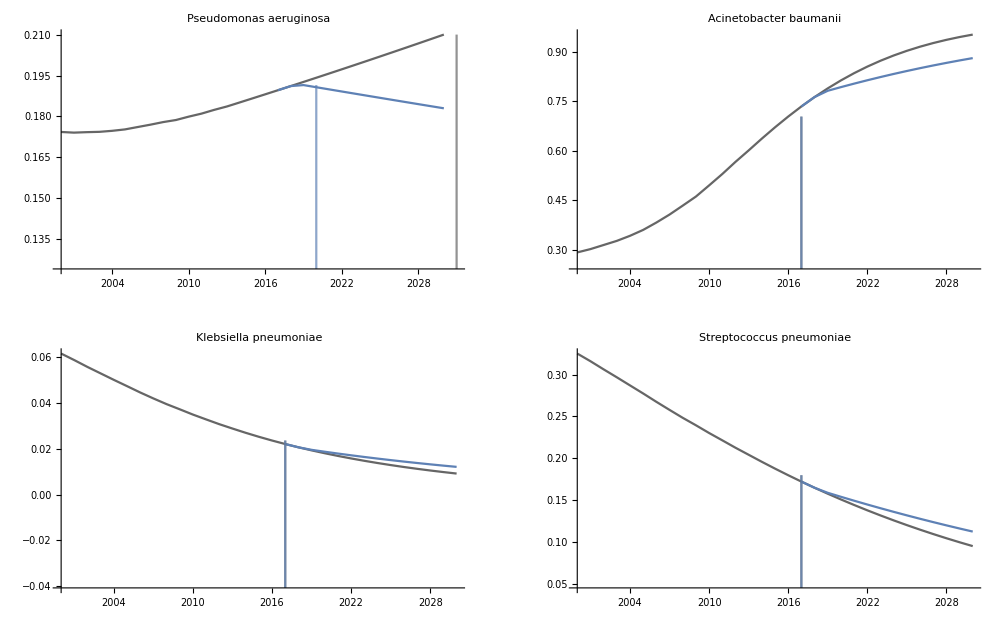
-Graphics-{Antibiotic Replacement Year Under Various Interventions}

```mathematica
plotSQy=Table[ListLinePlot[sqdata[[i]][[19;;]],FrameLabel->{{x,Year},{y,Resistance}},PlotStyle->{GrayLevel[0.4],Thick},PlotLabel->Style[pathogens[[i]],Italic,16],PlotRange->All,AxesOrigin-> {years[[1]],0}],{i,1,nop}];

switchplots=Panel[GraphicsGrid[{{Show[plotSQf[[1]],plotIf[[1]],yearSQ[[1]],yearI[[1]],
AxesStyle->Directive[14],AxesOrigin-> {years[[1]],ymin[[1]]},PlotRange->All],

Show[plotSQf[[2]],plotIf[[2]],yearSQ[[2]],yearI[[2]],PlotRange->All,Axes->True,AxesStyle->Directive[14],AxesOrigin->{years[[1]],ymin[[2]]}]},

{Show[plotSQf[[3]],plotIf[[3]],yearSQ[[3]],yearI[[3]],AxesStyle->Directive[14],AxesOrigin-> {years[[1]],ymin[[3]]},PlotRange->All],

Show[plotSQf[[4]],plotIf[[4]],yearSQ[[4]],yearI[[4]],AxesStyle->Directive[14],AxesOrigin-> {years[[1]],ymin[[4]]},PlotRange->All]}},ImageSize->1000],

{Style["Antibiotic Replacement Year Under Various Interventions","Panel",24,Background->White]}]
```

### Respiratory Isolates Total

```mathematica
resp=Import["resp model.xls"];
(*Years*)
years=data[[1]];
ti=years[[-1]]; (*start of projections*)
tf=2030; (*end of projections*)
pyears=Range[ti,tf];
```

```mathematica
respdistr=Table[Mean[resp[[2]][[i]][[-5;;-2]]],{i,1,nop}]; (*# isolates per pathogen averaged over last 2 years of data*)

(*MODEL FIT*)
respM=Total[Table[resp[[4]][[i]]*(respdistr[[i]]/Total[respdistr]),{i,1,nop}] ];(*total resistance for resp isolates weighted by # isolates/total for last year available*)

(*SQ PROJECTIONS*)
respSQ=Total[Table[resp[[6]][[i]]*(respdistr[[i]]/Total[respdistr]),{i,1,nop}] ];

(*I PROJECTIONS*)
respI=Total[Table[resp[[8]][[i]]*(respdistr[[i]]/Total[respdistr]),{i,1,nop}] ];
```

#### Plots

```mathematica
respD=Total[resp[[1]]]/Total[resp[[2]]]; (*raw data totaled across pathogens*)
plotrD=ListPlot[Transpose@{years,respD}, PlotStyle->{{Black, PointSize[Large]}}, PlotRange-> All, AxesOrigin-> {years[[1]],0}]; (*DATA*)
plotrM=ListLinePlot[Transpose@{years,respM},PlotStyle->{GrayLevel[0.4],Thick},AxesStyle->Directive[14],PlotRange->All,AxesOrigin-> {years[[1]],0}]; (*MODEL*)
plotrSQ=ListLinePlot[Transpose@{pyears,respSQ},PlotStyle->{GrayLevel[0.4],Thick,Dashed},AxesStyle->Directive[14],PlotRange->All,AxesOrigin-> {years[[1]],0}];(*SQ PROJECTIONS*)
plotrI=ListLinePlot[Transpose@{pyears,respI},PlotStyle->{CMYKColor[0.83,0.45,0.16,0.24],Thick},AxesStyle->Directive[14],PlotRange->All,AxesOrigin-> {years[[1]],0}];(*I PROJECTIONS*)

respplot=Show[plotrD,plotrM,plotrSQ,plotrI,PlotRange-> {{years[[1]],tf},{respM[[1]]-0.1,respSQ[[-1]]+0.1}},AxesOrigin-> {years[[1]],respM[[1]]-0.1},LabelStyle-> Directive[Black,14],PlotLabel->Style["Resistance Frequency Among Respiratory Isolates",Black, Italic, 16],ImageSize-> 500];
```

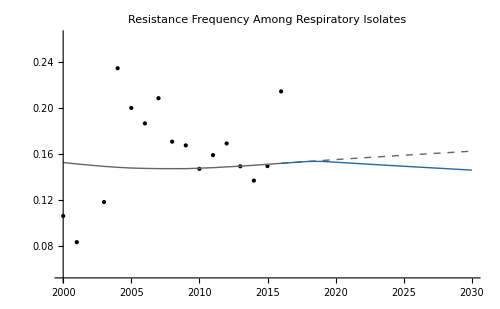

```mathematica
respplot
```